# CHSH game

Uncover potential of quantum correlations

## Example Content

One feature of quantum correlations is that one can do computations beyond the best classical approach. It is also the core idea behind Bell's theorem, which reflect directly on CHSH game.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

In CHSH game, a referee (Charlie) sends two random binary numbers (x and y) to Alice and Bob, while they should report two binary numbers (a and b). The winning cases happen if x∧y=a⊻b. Alice and Bob cannot communicate during the game, but they can decide on a strategy before hand. They can use a Bell state (i.e., an entangled quantum state) and by conditioning their local operations on that state, the results they report can go beyond the best classical strategy.

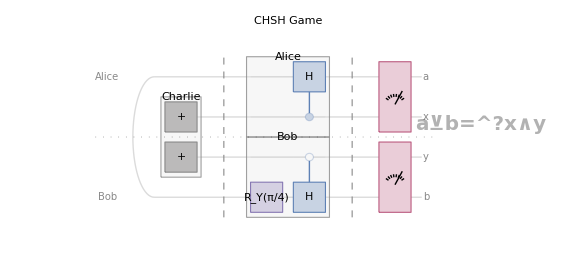

```mathematica
QuantumCircuitOperator["CHSH"]["Diagram",]
```

One can generate the multivariate probability distribution of quantum measurements as follows.

```mathematica
QuantumCircuitOperator["CHSH"][]["MultivariateDistribution"]
```

CategoricalDistribution[…]

Corresponding probability table:

```mathematica
Information[QuantumCircuitOperator["CHSH"][]["MultivariateDistribution"],"ProbabilityTable"]
```

The winning probabiity can be directly computed under the assumption that outcomes follow the corresponding quantum probability distribution.

```mathematica
NProbability[BitAnd[x,y]==BitXor[a,b],{a,x,y,b}\[Distributed]QuantumCircuitOperator["CHSH"][]["MultivariateDistribution"]]
```

0.853553

As one can see, it is more that the best classical approach (which gives 75% change of winning).

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

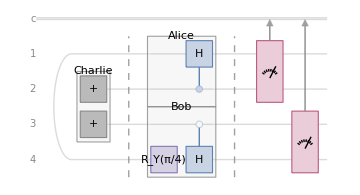

```mathematica
QuantumCircuitOperator["CHSH"]["Diagram"]
```

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

keyword 1

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.